# Paper Figures

## Figure 1: Throughput / BatchSize AlexNet

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
rawDs=Dataset[$DurationInformation]
```

Dataset[<>]

```mathematica
mean=TrimmedMean[#,0.2]&;
query=Query[GroupBy["Framework"],SortBy["BatchSize"],{"Framework","Model","ModelVersion","HostName","UsingGPU","MachineArchitecture","BatchSize","Durations"}];
```

```mathematica
ds=query[$DurationInformation];
ds=Association@KeyValueMap[
Function[{key,val},
key->With[{
cols=Values@GroupBy[val,StringRiffle[ToString/@Most[Values@#],"/"]&]
},
Table[
With[{
fcol=col[[1]],
durations=Lookup[col,"Durations"]
},
With[{
duration=Min[mean/@durations]
},
(*/*mean,(mean[#Durations]/(#BatchSize*10^3))&,(#BatchSize*10^3/mean[#Durations])&}*)
Join[
Most[fcol],
<|
"Duration"->duration,
"Latency"->(fcol["BatchSize"]*10^3)/duration,
"Throughput"->duration/(fcol["BatchSize"]*10^3)
|>
]
]
],
{col,cols}
]]
],
ds
];
```

```mathematica
ds[[1]]
```

{<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→2441.09,Latency→0.409653,Throughput→2.44109|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→5101.73,Latency→0.196012,Throughput→5.10173|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→1958.55,Latency→0.510583,Throughput→1.95855|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→3421.09,Latency→0.584609,Throughput→1.71055|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→7939.55,Latency→0.251904,Throughput→3.96977|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→2341.73,Latency→0.85407,Throughput→1.17086|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→5392.17,Latency→0.741817,Throughput→1.34804|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→3389.96,Latency→1.17996,Throughput→0.84749|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→12356.9,Latency→0.323706,Throughput→3.08923|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→9677.52,Latency→0.826658,Throughput→1.20969|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→5668.27,Latency→1.41136,Throughput→0.708534|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→18030.6,Latency→0.443689,Throughput→2.25383|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→15320.3,Latency→1.04436,Throughput→0.957522|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→9817.09,Latency→1.62981,Throughput→0.613568|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→30024.9,Latency→0.532891,Throughput→1.87656|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→30049.1,Latency→1.06492,Throughput→0.939034|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→18994.1,Latency→1.68474,Throughput→0.593564|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→52702.2,Latency→0.607185,Throughput→1.64694|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→59202.7,Latency→1.08103,Throughput→0.925042|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→39221.1,Latency→1.63177,Throughput→0.61283|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→103415.,Latency→0.618865,Throughput→1.61586|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→123164.,Latency→1.03926,Throughput→0.962219|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→88251.,Latency→1.45041,Throughput→0.689461|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→208826.,Latency→0.61295,Throughput→1.63145|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→249693.,Latency→1.02526,Throughput→0.975364|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→217907.,Latency→1.17481,Throughput→0.8512|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→411637.,Latency→0.621908,Throughput→1.60796|>}

```mathematica
Dataset[ds]
```

Dataset[<>]

#### Processed Data

```mathematica
ds
```

<|MXNet→{<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→2441.09,Latency→0.409653,Throughput→2.44109|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→5101.73,Latency→0.196012,Throughput→5.10173|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→1958.55,Latency→0.510583,Throughput→1.95855|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→3421.09,Latency→0.584609,Throughput→1.71055|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→7939.55,Latency→0.251904,Throughput→3.96977|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→2341.73,Latency→0.85407,Throughput→1.17086|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→5392.17,Latency→0.741817,Throughput→1.34804|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→3389.96,Latency→1.17996,Throughput→0.84749|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→12356.9,Latency→0.323706,Throughput→3.08923|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→9677.52,Latency→0.826658,Throughput→1.20969|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→5668.27,Latency→1.41136,Throughput→0.708534|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→18030.6,Latency→0.443689,Throughput→2.25383|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→15320.3,Latency→1.04436,Throughput→0.957522|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→9817.09,Latency→1.62981,Throughput→0.613568|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→30024.9,Latency→0.532891,Throughput→1.87656|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→30049.1,Latency→1.06492,Throughput→0.939034|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→18994.1,Latency→1.68474,Throughput→0.593564|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→52702.2,Latency→0.607185,Throughput→1.64694|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→59202.7,Latency→1.08103,Throughput→0.925042|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→39221.1,Latency→1.63177,Throughput→0.61283|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→103415.,Latency→0.618865,Throughput→1.61586|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→123164.,Latency→1.03926,Throughput→0.962219|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→88251.,Latency→1.45041,Throughput→0.689461|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→208826.,Latency→0.61295,Throughput→1.63145|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→249693.,Latency→1.02526,Throughput→0.975364|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→217907.,Latency→1.17481,Throughput→0.8512|>,<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→411637.,Latency→0.621908,Throughput→1.60796|>},Caffe2→{<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→8883.73,Latency→0.112565,Throughput→8.88373|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→9752.73,Latency→0.102535,Throughput→9.75273|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→12837.8,Latency→0.0778949,Throughput→12.8378|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→13915.3,Latency→0.143727,Throughput→6.95764|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→16298.7,Latency→0.122709,Throughput→8.14936|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→20465.5,Latency→0.0977257,Throughput→10.2327|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→17874.1,Latency→0.223787,Throughput→4.46853|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→28515.7,Latency→0.140274,Throughput→7.12892|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→33838.3,Latency→0.118209,Throughput→8.45957|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→26193.5,Latency→0.305419,Throughput→3.27419|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→52943.3,Latency→0.151105,Throughput→6.61792|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→61797.6,Latency→0.129455,Throughput→7.7247|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→49875.7,Latency→0.320797,Throughput→3.11723|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→101253.,Latency→0.15802,Throughput→6.32832|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→120254.,Latency→0.133052,Throughput→7.51588|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→100682.,Latency→0.317832,Throughput→3.14631|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→198339.,Latency→0.16134,Throughput→6.19811|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→212710.,Latency→0.15044,Throughput→6.64718|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→213046.,Latency→0.300405,Throughput→3.32884|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→397290.,Latency→0.161091,Throughput→6.20766|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→428181.,Latency→0.14947,Throughput→6.69032|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→430287.,Latency→0.297476,Throughput→3.36162|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→806496.,Latency→0.158711,Throughput→6.30075|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→878439.,Latency→0.145713,Throughput→6.8628|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→876597.,Latency→0.292039,Throughput→3.42421|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→1.65895×10^6,Latency→0.154315,Throughput→6.48026|>,<|Framework→Caffe2,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→1.74029×10^6,Latency→0.147102,Throughput→6.79799|>},Caffe→{<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→7882.91,Latency→0.126857,Throughput→7.88291|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→6756.36,Latency→0.148009,Throughput→6.75636|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→11541.6,Latency→0.0866428,Throughput→11.5416|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→13490.3,Latency→0.148255,Throughput→6.74514|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→10435.4,Latency→0.191656,Throughput→5.21768|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→17477.1,Latency→0.114436,Throughput→8.73855|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→24953.9,Latency→0.160296,Throughput→6.23848|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→16957.5,Latency→0.235883,Throughput→4.23939|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→27061.5,Latency→0.147812,Throughput→6.76536|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→48103.3,Latency→0.166309,Throughput→6.01291|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→23886.,Latency→0.334924,Throughput→2.98575|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→50361.9,Latency→0.15885,Throughput→6.29524|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→96350.8,Latency→0.16606,Throughput→6.02193|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→43808.5,Latency→0.365226,Throughput→2.73803|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→97756.1,Latency→0.163673,Throughput→6.10976|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→186867.,Latency→0.171245,Throughput→5.83959|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→100885.,Latency→0.317194,Throughput→3.15265|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→186571.,Latency→0.171516,Throughput→5.83034|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→379126.,Latency→0.16881,Throughput→5.92384|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→190835.,Latency→0.335369,Throughput→2.98179|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→366206.,Latency→0.174765,Throughput→5.72197|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→757214.,Latency→0.169041,Throughput→5.91573|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→375151.,Latency→0.341196,Throughput→2.93087|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→742905.,Latency→0.172297,Throughput→5.80395|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→1.48994×10^6,Latency→0.171819,Throughput→5.82009|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→741584.,Latency→0.345207,Throughput→2.89681|>,<|Framework→Caffe,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→1.4785×10^6,Latency→0.173149,Throughput→5.77538|>}|>

#### Visualization

```mathematica
plotOpts={
PlotMarkers->{Automatic,Medium},
PlotRange->All,
ImageSize->600,
Frame->True,
PlotRangeClipping->False,
PlotTheme->{"FullAxesGrid","LargeLabels"},
PlotLegends->PointLegend["Expressions",{Center,Bottom},Joined->True,LegendLayout->"Row",ImageSize->{550,All},LegendFunction->(Framed[#,ImageMargins->{{40,0},{0,0}},ImageSize->{550,All}]&)]
};
```

```mathematica
ds[[1,1]]
```

<|Framework→MXNet,Model→BVLC-AlexNet,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→2441.09,Latency→0.409653,Throughput→2.44109|>

```mathematica
mxnetQuery=Query["MXNet"];
caffe2Query=Query["Caffe2"];
caffeQuery=Query["Caffe"];
amd64Selector=#["MachineArchitecture"]==="amd64"&;
amd64WhateverSelector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="whatever"&;
amd64Impact2Selector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="impact2"&;
ppcSelector=#["MachineArchitecture"]==="ppc64le"&;
getBatchLatency[x_]:=Lookup[x,{"BatchSize","Latency"}];
getBatchThroughput[x_]:=Lookup[x,{"BatchSize","Throughput"}];
```

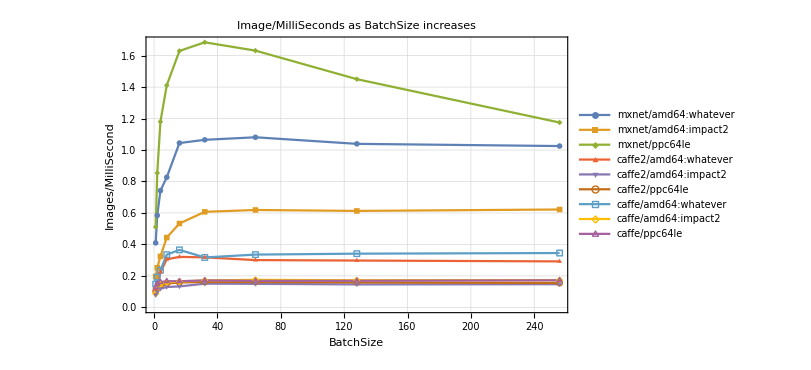

```mathematica
ListLinePlot[{
Legended[getBatchLatency/@Select[mxnetQuery[ds],amd64WhateverSelector],"mxnet/amd64:whatever"],
Legended[getBatchLatency/@Select[mxnetQuery[ds],amd64Impact2Selector],"mxnet/amd64:impact2"],
Legended[getBatchLatency/@Select[mxnetQuery[ds],ppcSelector],"mxnet/ppc64le"],
Legended[getBatchLatency/@Select[caffe2Query[ds],amd64WhateverSelector],"caffe2/amd64:whatever"],
Legended[getBatchLatency/@Select[caffe2Query[ds],amd64Impact2Selector],"caffe2/amd64:impact2"],
Legended[getBatchLatency/@Select[caffe2Query[ds],ppcSelector],"caffe2/ppc64le"],
Legended[getBatchLatency/@Select[caffeQuery[ds],amd64WhateverSelector],"caffe/amd64:whatever"],
Legended[getBatchLatency/@Select[caffeQuery[ds],amd64Impact2Selector],"caffe/amd64:impact2"],
Legended[getBatchLatency/@Select[caffeQuery[ds],ppcSelector],"caffe/ppc64le"]
},
Sequence[plotOpts],
FrameLabel->{"BatchSize","Images/MilliSecond"},
PlotLabel->"Image/MilliSeconds as BatchSize increases"
]
```

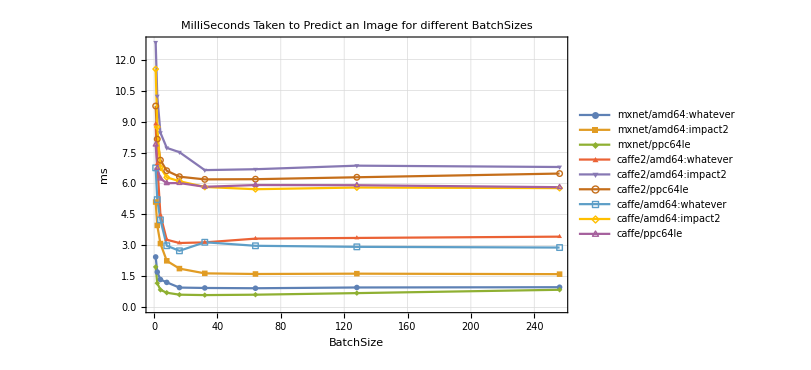

```mathematica
ListLinePlot[{
Legended[getBatchThroughput/@Select[mxnetQuery[ds],amd64WhateverSelector],"mxnet/amd64:whatever"],
Legended[getBatchThroughput/@Select[mxnetQuery[ds],amd64Impact2Selector],"mxnet/amd64:impact2"],
Legended[getBatchThroughput/@Select[mxnetQuery[ds],ppcSelector],"mxnet/ppc64le"],
Legended[getBatchThroughput/@Select[caffe2Query[ds],amd64WhateverSelector],"caffe2/amd64:whatever"],
Legended[getBatchThroughput/@Select[caffe2Query[ds],amd64Impact2Selector],"caffe2/amd64:impact2"],
Legended[getBatchThroughput/@Select[caffe2Query[ds],ppcSelector],"caffe2/ppc64le"],
Legended[getBatchThroughput/@Select[caffeQuery[ds],amd64WhateverSelector],"caffe/amd64:whatever"],
Legended[getBatchThroughput/@Select[caffeQuery[ds],amd64Impact2Selector],"caffe/amd64:impact2"],
Legended[getBatchThroughput/@Select[caffeQuery[ds],ppcSelector],"caffe/ppc64le"]
},
Sequence[plotOpts],
FrameLabel->{"BatchSize","ms"},
PlotLabel->"MilliSeconds Taken to Predict an Image for different BatchSizes"
]
```

## Figure 1: Throughput / BatchSize Resnet101

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
rawDs=Dataset[$DurationInformation]
```

Dataset[<>]

```mathematica
mean=TrimmedMean[#,0.2]&;
query=Query[GroupBy["Framework"],SortBy["BatchSize"],{"Framework","Model","ModelVersion","HostName","UsingGPU","MachineArchitecture","BatchSize","Durations"}];
```

```mathematica
ds=query[$DurationInformation];
ds=Association@KeyValueMap[
Function[{key,val},
key->With[{
cols=Values@GroupBy[val,StringRiffle[ToString/@Most[Values@#],"/"]&]
},
Table[
With[{
fcol=col[[1]],
durations=Lookup[col,"Durations"]
},
With[{
duration=Min[mean/@durations]
},
(*/*mean,(mean[#Durations]/(#BatchSize*10^3))&,(#BatchSize*10^3/mean[#Durations])&}*)
Join[
Most[fcol],
<|
"Duration"->duration,
"Latency"->(fcol["BatchSize"]*10^3)/duration,
"Throughput"->duration/(fcol["BatchSize"]*10^3)
|>
]
]
],
{col,cols}
]]
],
ds
];
```

```mathematica
Dataset[ds]
```

Dataset[<>]

#### Processed Data

```mathematica
ds
```

<|MXNet→{<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→13082.1,Latency→0.0764404,Throughput→13.0821|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→16804.9,Latency→0.0595064,Throughput→16.8049|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→31432.5,Latency→0.0318143,Throughput→31.4325|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→16206.8,Latency→0.123405,Throughput→8.10341|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→19116.3,Latency→0.104623,Throughput→9.55814|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→43425.4,Latency→0.046056,Throughput→21.7127|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→20558.,Latency→0.194572,Throughput→5.1395|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→23894.2,Latency→0.167405,Throughput→5.97355|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→68749.5,Latency→0.0581822,Throughput→17.1874|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→32529.4,Latency→0.245931,Throughput→4.06618|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→37510.8,Latency→0.213272,Throughput→4.68884|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→111635.,Latency→0.0716623,Throughput→13.9543|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→56519.8,Latency→0.283087,Throughput→3.53249|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→61457.6,Latency→0.260342,Throughput→3.8411|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→188485.,Latency→0.0848874,Throughput→11.7803|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→110054.,Latency→0.290765,Throughput→3.4392|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→112864.,Latency→0.283528,Throughput→3.52699|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→354441.,Latency→0.0902831,Throughput→11.0763|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→212321.,Latency→0.301431,Throughput→3.31751|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→215107.,Latency→0.297526,Throughput→3.36105|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→668597.,Latency→0.0957229,Throughput→10.4468|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→420383.,Latency→0.304484,Throughput→3.28425|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→426189.,Latency→0.300336,Throughput→3.3296|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→1.30363×10^6,Latency→0.0981871,Throughput→10.1846|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→840841.,Latency→0.304457,Throughput→3.28454|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→861099.,Latency→0.297294,Throughput→3.36367|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→2.59554×10^6,Latency→0.0986306,Throughput→10.1388|>},Caffe2→{<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→18034.3,Latency→0.05545,Throughput→18.0343|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→23033.4,Latency→0.0434153,Throughput→23.0334|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→39447.1,Latency→0.0253504,Throughput→39.4471|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→24809.3,Latency→0.080615,Throughput→12.4046|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→34829.3,Latency→0.057423,Throughput→17.4146|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→66705.5,Latency→0.0299825,Throughput→33.3528|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→38688.7,Latency→0.103389,Throughput→9.67218|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→56852.5,Latency→0.0703574,Throughput→14.2131|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→120080.,Latency→0.033311,Throughput→30.0201|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→68423.5,Latency→0.116919,Throughput→8.55294|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→102796.,Latency→0.0778238,Throughput→12.8495|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→230806.,Latency→0.0346612,Throughput→28.8507|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→133415.,Latency→0.119927,Throughput→8.33843|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→192537.,Latency→0.0831008,Throughput→12.0336|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→438552.,Latency→0.0364837,Throughput→27.4095|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→248275.,Latency→0.12889,Throughput→7.75858|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→371952.,Latency→0.0860326,Throughput→11.6235|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→735778.,Latency→0.0869828,Throughput→11.4965|>},Caffe→{<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→41144.5,Latency→0.0243046,Throughput→41.1445|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→25720.6,Latency→0.0388793,Throughput→25.7206|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→82964.5,Latency→0.0120534,Throughput→82.9645|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→52668.1,Latency→0.0379737,Throughput→26.334|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→37073.5,Latency→0.053947,Throughput→18.5367|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→95938.,Latency→0.0208468,Throughput→47.969|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→73953.5,Latency→0.0540881,Throughput→18.4884|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→48733.3,Latency→0.0820794,Throughput→12.1833|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→135401.,Latency→0.0295418,Throughput→33.8503|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→107664.,Latency→0.0743055,Throughput→13.458|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→74760.7,Latency→0.107008,Throughput→9.34509|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→214475.,Latency→0.0373004,Throughput→26.8094|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→176407.,Latency→0.0906995,Throughput→11.0254|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→125972.,Latency→0.127012,Throughput→7.87327|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→372426.,Latency→0.0429616,Throughput→23.2766|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→325340.,Latency→0.0983585,Throughput→10.1669|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→239284.,Latency→0.133732,Throughput→7.47763|>}|>

#### Visualization

```mathematica
plotOpts={
PlotMarkers->{Automatic,Medium},
PlotRange->All,
ImageSize->600,
Frame->True,
PlotRangeClipping->False,
PlotTheme->{"FullAxesGrid","LargeLabels"},
PlotLegends->PointLegend["Expressions",{Center,Bottom},Joined->True,LegendLayout->"Row",ImageSize->{550,All},LegendFunction->(Framed[#,ImageMargins->{{40,0},{0,0}},ImageSize->{550,All}]&)]
};
```

```mathematica
mxnetQuery=Query["MXNet"];
caffe2Query=Query["Caffe2"];
caffeQuery=Query["Caffe"];
amd64Selector=#["MachineArchitecture"]==="amd64"&;
amd64WhateverSelector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="whatever"&;
amd64Impact2Selector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="impact2"&;
ppcSelector=#["MachineArchitecture"]==="ppc64le"&;
getBatchLatency[x_]:=Lookup[x,{"BatchSize","Latency"}];
getBatchThroughput[x_]:=Lookup[x,{"BatchSize","Throughput"}];
```

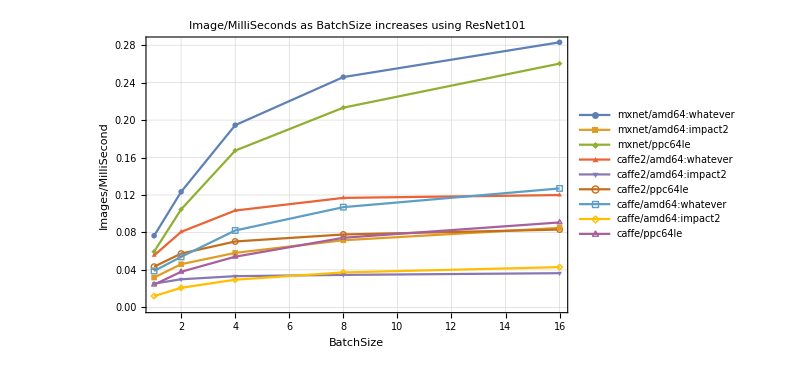

```mathematica
upto5=Take[#,UpTo[5]]&;
ListLinePlot[{
Legended[getBatchLatency/@upto5@Select[mxnetQuery[ds],amd64WhateverSelector],"mxnet/amd64:whatever"],
Legended[getBatchLatency/@upto5@Select[mxnetQuery[ds],amd64Impact2Selector],"mxnet/amd64:impact2"],
Legended[getBatchLatency/@upto5@Select[mxnetQuery[ds],ppcSelector],"mxnet/ppc64le"],
Legended[getBatchLatency/@upto5@Select[caffe2Query[ds],amd64WhateverSelector],"caffe2/amd64:whatever"],
Legended[getBatchLatency/@upto5@Select[caffe2Query[ds],amd64Impact2Selector],"caffe2/amd64:impact2"],
Legended[getBatchLatency/@upto5@Select[caffe2Query[ds],ppcSelector],"caffe2/ppc64le"],
Legended[getBatchLatency/@upto5@Select[caffeQuery[ds],amd64WhateverSelector],"caffe/amd64:whatever"],
Legended[getBatchLatency/@upto5@Select[caffeQuery[ds],amd64Impact2Selector],"caffe/amd64:impact2"],
Legended[getBatchLatency/@upto5@Select[caffeQuery[ds],ppcSelector],"caffe/ppc64le"]
},
Sequence[plotOpts],
FrameLabel->{"BatchSize","Images/MilliSecond"},
PlotLabel->"Image/MilliSeconds as BatchSize increases using ResNet101"
]
```

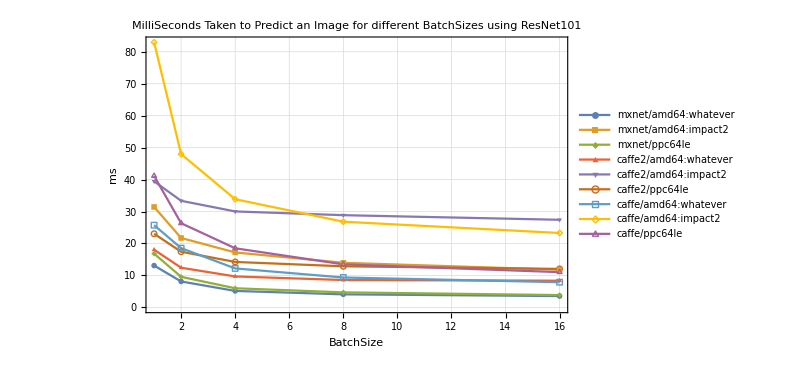

```mathematica
ListLinePlot[{
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],amd64WhateverSelector],"mxnet/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],amd64Impact2Selector],"mxnet/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],ppcSelector],"mxnet/ppc64le"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],amd64WhateverSelector],"caffe2/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],amd64Impact2Selector],"caffe2/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],ppcSelector],"caffe2/ppc64le"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],amd64WhateverSelector],"caffe/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],amd64Impact2Selector],"caffe/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],ppcSelector],"caffe/ppc64le"]
},
Sequence[plotOpts],
FrameLabel->{"BatchSize","ms"},
PlotLabel->"MilliSeconds Taken to Predict an Image for different BatchSizes using ResNet101"
]
```

## Figure 1: Throughput / BatchSize Resnet101 (CPU)

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
rawDs=Dataset[$DurationInformation]
```

Dataset[<>]

```mathematica
ClearAll[mean];
mean[x_]:=If[x==={},0,TrimmedMean[x,.2]];
query=Query[GroupBy["Framework"],SortBy["BatchSize"],{"ID","Framework","Model","ModelVersion","HostName","UsingGPU","MachineArchitecture","BatchSize","Durations"}];
```

```mathematica
ds=query[$DurationInformation];
ds=Association@KeyValueMap[
Function[{key,val},
key->With[{
cols=Values@GroupBy[val,StringRiffle[ToString/@Rest[Most[Values@#]],"/"]&]
},
Table[
With[{
fcol=col[[1]],
durations=Lookup[col,"Durations"]
},
With[{
duration=Min[mean/@durations]
},
(*/*mean,(mean[#Durations]/(#BatchSize*10^3))&,(#BatchSize*10^3/mean[#Durations])&}*)
Join[
Most[fcol],
<|
"Duration"->duration,
"Latency"->(fcol["BatchSize"]*10^3)/duration,
"Throughput"->duration/(fcol["BatchSize"]*10^3)
|>
]
]
],
{col,cols}
]]
],
ds
];
```

#### Processed Data

```mathematica
ds
```

<|MXNet→{<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→13082.1,Latency→0.0764404,Throughput→13.0821|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→16804.9,Latency→0.0595064,Throughput→16.8049|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→31432.5,Latency→0.0318143,Throughput→31.4325|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→16206.8,Latency→0.123405,Throughput→8.10341|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→19116.3,Latency→0.104623,Throughput→9.55814|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→43425.4,Latency→0.046056,Throughput→21.7127|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→20558.,Latency→0.194572,Throughput→5.1395|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→23894.2,Latency→0.167405,Throughput→5.97355|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→68749.5,Latency→0.0581822,Throughput→17.1874|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→32529.4,Latency→0.245931,Throughput→4.06618|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→37510.8,Latency→0.213272,Throughput→4.68884|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→111635.,Latency→0.0716623,Throughput→13.9543|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→56519.8,Latency→0.283087,Throughput→3.53249|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→61457.6,Latency→0.260342,Throughput→3.8411|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→188485.,Latency→0.0848874,Throughput→11.7803|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→110054.,Latency→0.290765,Throughput→3.4392|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→112864.,Latency→0.283528,Throughput→3.52699|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→354441.,Latency→0.0902831,Throughput→11.0763|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→212321.,Latency→0.301431,Throughput→3.31751|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→215107.,Latency→0.297526,Throughput→3.36105|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→668597.,Latency→0.0957229,Throughput→10.4468|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→420383.,Latency→0.304484,Throughput→3.28425|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→426189.,Latency→0.300336,Throughput→3.3296|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→1.30363×10^6,Latency→0.0981871,Throughput→10.1846|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→840841.,Latency→0.304457,Throughput→3.28454|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→861099.,Latency→0.297294,Throughput→3.36367|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→2.59554×10^6,Latency→0.0986306,Throughput→10.1388|>},Caffe2→{<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→18034.3,Latency→0.05545,Throughput→18.0343|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→23033.4,Latency→0.0434153,Throughput→23.0334|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→39447.1,Latency→0.0253504,Throughput→39.4471|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→24809.3,Latency→0.080615,Throughput→12.4046|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→34829.3,Latency→0.057423,Throughput→17.4146|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→66705.5,Latency→0.0299825,Throughput→33.3528|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→38688.7,Latency→0.103389,Throughput→9.67218|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→56852.5,Latency→0.0703574,Throughput→14.2131|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→120080.,Latency→0.033311,Throughput→30.0201|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→68423.5,Latency→0.116919,Throughput→8.55294|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→102796.,Latency→0.0778238,Throughput→12.8495|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→230806.,Latency→0.0346612,Throughput→28.8507|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→133415.,Latency→0.119927,Throughput→8.33843|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→192537.,Latency→0.0831008,Throughput→12.0336|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→438552.,Latency→0.0364837,Throughput→27.4095|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→248275.,Latency→0.12889,Throughput→7.75858|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→371952.,Latency→0.0860326,Throughput→11.6235|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→735778.,Latency→0.0869828,Throughput→11.4965|>},Caffe→{<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→41144.5,Latency→0.0243046,Throughput→41.1445|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→25720.6,Latency→0.0388793,Throughput→25.7206|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→82964.5,Latency→0.0120534,Throughput→82.9645|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→52668.1,Latency→0.0379737,Throughput→26.334|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→37073.5,Latency→0.053947,Throughput→18.5367|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→95938.,Latency→0.0208468,Throughput→47.969|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→73953.5,Latency→0.0540881,Throughput→18.4884|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→48733.3,Latency→0.0820794,Throughput→12.1833|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→135401.,Latency→0.0295418,Throughput→33.8503|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→107664.,Latency→0.0743055,Throughput→13.458|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→74760.7,Latency→0.107008,Throughput→9.34509|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→214475.,Latency→0.0373004,Throughput→26.8094|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→176407.,Latency→0.0906995,Throughput→11.0254|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→125972.,Latency→0.127012,Throughput→7.87327|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→372426.,Latency→0.0429616,Throughput→23.2766|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→325340.,Latency→0.0983585,Throughput→10.1669|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→239284.,Latency→0.133732,Throughput→7.47763|>}|>

#### Visualization

```mathematica
plotOpts={
PlotMarkers->{Automatic,Medium},
PlotRange->All,
ImageSize->600,
Frame->True,
PlotRangeClipping->False,
PlotTheme->{"FullAxesGrid","LargeLabels"},
PlotLegends->PointLegend["Expressions",{Center,Bottom},Joined->True,LegendLayout->"Row",ImageSize->{550,All},LegendFunction->(Framed[#,ImageMargins->{{40,0},{0,0}},ImageSize->{550,All}]&)]
};
```

```mathematica
mxnetQuery=Query["MXNet"];
caffe2Query=Query["Caffe2"];
caffeQuery=Query["Caffe"];
amd64Selector=#["MachineArchitecture"]==="amd64"&;
amd64WhateverSelector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="whatever"&;
amd64Impact2Selector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="impact2"&;
ppcSelector=#["MachineArchitecture"]==="ppc64le"&;
getBatchLatency0[x_]:=Lookup[x,{"Framework","Model","ModelVersion","Latency"}];
getBatchThroughput0[x_]:=Lookup[x,{"Framework","Model","ModelVersion","Throughput"}];
getBatchLatency[x_]:=Tooltip[x["Latency"],GeneralUtilities`Infobox[x,"Information"]];
getBatchThroughput[x_]:=Tooltip[x["Throughput"],Lookup[x,{"Framework","Model","ModelVersion","Throughput"}]];
```

```mathematica
upto5=Take[#,UpTo[5]]&;
sort[x_]:=SortBy[x,Lookup[#,"Model"]<>ToString[Lookup[#,"ModelVersion"]]&];
BarChart[{
Callout[getBatchLatency/@Select[sort[mxnetQuery[ds]],amd64WhateverSelector],"mxnet/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[mxnetQuery[ds]],ppcSelector],"mxnet/ppc64le"],
Callout[getBatchLatency/@Select[sort[caffe2Query[ds]],amd64WhateverSelector],"caffe2/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[caffe2Query[ds]],ppcSelector],"caffe2/ppc64le"],
Callout[getBatchLatency/@Select[sort[caffeQuery[ds]],amd64WhateverSelector],"caffe/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[caffeQuery[ds]],ppcSelector],"caffe/ppc64le"]
},
(*Sequence[plotOpts],*)
FrameLabel->{"BatchSize","Images/MilliSecond"},
PlotLabel->"Image/MilliSeconds as BatchSize increases using ResNet101",
BarSpacing->{Automatic,1},
PlotTheme->"Detailed"
]
```

-Graphics-

## Figure 1: Throughput / BatchSize Resnet101 (_CPU)

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
rawDs=Dataset[$DurationInformation]
```

Dataset[<>]

```mathematica
ClearAll[mean];
mean[x_]:=If[x==={},0,TrimmedMean[x,.2]];
query=Query[GroupBy["Framework"],SortBy["BatchSize"],{"ID","Framework","Model","ModelVersion","HostName","UsingGPU","MachineArchitecture","BatchSize","Durations"}];
```

```mathematica
ds=query[$DurationInformation];
ds=Association@KeyValueMap[
Function[{key,val},
key->With[{
cols=Values@GroupBy[val,StringRiffle[ToString/@Rest[Most[Values@#]],"/"]&]
},
Table[
With[{
fcol=col[[1]],
durations=Lookup[col,"Durations"]
},
With[{
duration=Min[mean/@durations]
},
(*/*mean,(mean[#Durations]/(#BatchSize*10^3))&,(#BatchSize*10^3/mean[#Durations])&}*)
Join[
Most[fcol],
<|
"Duration"->duration,
"Latency"->(fcol["BatchSize"]*10^3)/duration,
"Throughput"->duration/(fcol["BatchSize"]*10^3)
|>
]
]
],
{col,cols}
]]
],
ds
];
```

#### Processed Data

```mathematica
ds
```

<|MXNet→{<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→13082.1,Latency→0.0764404,Throughput→13.0821|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→16804.9,Latency→0.0595064,Throughput→16.8049|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→31432.5,Latency→0.0318143,Throughput→31.4325|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→16206.8,Latency→0.123405,Throughput→8.10341|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→19116.3,Latency→0.104623,Throughput→9.55814|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→43425.4,Latency→0.046056,Throughput→21.7127|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→20558.,Latency→0.194572,Throughput→5.1395|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→23894.2,Latency→0.167405,Throughput→5.97355|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→68749.5,Latency→0.0581822,Throughput→17.1874|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→32529.4,Latency→0.245931,Throughput→4.06618|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→37510.8,Latency→0.213272,Throughput→4.68884|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→111635.,Latency→0.0716623,Throughput→13.9543|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→56519.8,Latency→0.283087,Throughput→3.53249|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→61457.6,Latency→0.260342,Throughput→3.8411|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→188485.,Latency→0.0848874,Throughput→11.7803|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→110054.,Latency→0.290765,Throughput→3.4392|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→112864.,Latency→0.283528,Throughput→3.52699|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→354441.,Latency→0.0902831,Throughput→11.0763|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→212321.,Latency→0.301431,Throughput→3.31751|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→215107.,Latency→0.297526,Throughput→3.36105|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→64,Duration→668597.,Latency→0.0957229,Throughput→10.4468|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→420383.,Latency→0.304484,Throughput→3.28425|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→128,Duration→426189.,Latency→0.300336,Throughput→3.3296|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→128,Duration→1.30363×10^6,Latency→0.0981871,Throughput→10.1846|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→840841.,Latency→0.304457,Throughput→3.28454|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→256,Duration→861099.,Latency→0.297294,Throughput→3.36367|>,<|Framework→MXNet,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→256,Duration→2.59554×10^6,Latency→0.0986306,Throughput→10.1388|>},Caffe2→{<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→18034.3,Latency→0.05545,Throughput→18.0343|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→23033.4,Latency→0.0434153,Throughput→23.0334|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→39447.1,Latency→0.0253504,Throughput→39.4471|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→24809.3,Latency→0.080615,Throughput→12.4046|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→34829.3,Latency→0.057423,Throughput→17.4146|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→66705.5,Latency→0.0299825,Throughput→33.3528|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→38688.7,Latency→0.103389,Throughput→9.67218|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→56852.5,Latency→0.0703574,Throughput→14.2131|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→120080.,Latency→0.033311,Throughput→30.0201|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→68423.5,Latency→0.116919,Throughput→8.55294|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→102796.,Latency→0.0778238,Throughput→12.8495|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→230806.,Latency→0.0346612,Throughput→28.8507|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→133415.,Latency→0.119927,Throughput→8.33843|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→192537.,Latency→0.0831008,Throughput→12.0336|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→438552.,Latency→0.0364837,Throughput→27.4095|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→248275.,Latency→0.12889,Throughput→7.75858|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→371952.,Latency→0.0860326,Throughput→11.6235|>,<|Framework→Caffe2,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→64,Duration→735778.,Latency→0.0869828,Throughput→11.4965|>},Caffe→{<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→1,Duration→41144.5,Latency→0.0243046,Throughput→41.1445|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→25720.6,Latency→0.0388793,Throughput→25.7206|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→1,Duration→82964.5,Latency→0.0120534,Throughput→82.9645|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→2,Duration→52668.1,Latency→0.0379737,Throughput→26.334|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→37073.5,Latency→0.053947,Throughput→18.5367|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→2,Duration→95938.,Latency→0.0208468,Throughput→47.969|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→4,Duration→73953.5,Latency→0.0540881,Throughput→18.4884|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→48733.3,Latency→0.0820794,Throughput→12.1833|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→4,Duration→135401.,Latency→0.0295418,Throughput→33.8503|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→8,Duration→107664.,Latency→0.0743055,Throughput→13.458|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→74760.7,Latency→0.107008,Throughput→9.34509|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→8,Duration→214475.,Latency→0.0373004,Throughput→26.8094|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→16,Duration→176407.,Latency→0.0906995,Throughput→11.0254|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→125972.,Latency→0.127012,Throughput→7.87327|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→impact2,UsingGPU→True,MachineArchitecture→amd64,BatchSize→16,Duration→372426.,Latency→0.0429616,Throughput→23.2766|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→minsky1,UsingGPU→True,MachineArchitecture→ppc64le,BatchSize→32,Duration→325340.,Latency→0.0983585,Throughput→10.1669|>,<|Framework→Caffe,Model→ResNet101,ModelVersion→1.0,HostName→whatever,UsingGPU→True,MachineArchitecture→amd64,BatchSize→32,Duration→239284.,Latency→0.133732,Throughput→7.47763|>}|>

#### Visualization

```mathematica
plotOpts={
PlotMarkers->{Automatic,Medium},
PlotRange->All,
ImageSize->600,
Frame->True,
PlotRangeClipping->False,
PlotTheme->{"FullAxesGrid","LargeLabels"},
PlotLegends->PointLegend["Expressions",{Center,Bottom},Joined->True,LegendLayout->"Row",ImageSize->{550,All},LegendFunction->(Framed[#,ImageMargins->{{40,0},{0,0}},ImageSize->{550,All}]&)]
};
```

```mathematica
mxnetQuery=Query["MXNet"];
caffe2Query=Query["Caffe2"];
caffeQuery=Query["Caffe"];
amd64Selector=#["MachineArchitecture"]==="amd64"&;
amd64WhateverSelector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="whatever"&;
amd64Impact2Selector=#["MachineArchitecture"]==="amd64"&&#["HostName"]==="impact2"&;
ppcSelector=#["MachineArchitecture"]==="ppc64le"&;
getBatchLatency0[x_]:=Lookup[x,{"Framework","Model","ModelVersion","Latency"}];
getBatchThroughput0[x_]:=Lookup[x,{"Framework","Model","ModelVersion","Throughput"}];
getBatchLatency[x_]:=Tooltip[x["Latency"],GeneralUtilities`Infobox[x,"Information"]];
getBatchThroughput[x_]:=Tooltip[x["Throughput"],Lookup[x,{"Framework","Model","ModelVersion","Throughput"}]];
```

```mathematica
upto5=Take[#,UpTo[5]]&;
sort[x_]:=SortBy[x,Lookup[#,"Model"]<>ToString[Lookup[#,"ModelVersion"]]&];
BarChart[{
Callout[getBatchLatency/@Select[sort[mxnetQuery[ds]],amd64WhateverSelector],"mxnet/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[mxnetQuery[ds]],ppcSelector],"mxnet/ppc64le"],
Callout[getBatchLatency/@Select[sort[caffe2Query[ds]],amd64WhateverSelector],"caffe2/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[caffe2Query[ds]],ppcSelector],"caffe2/ppc64le"],
Callout[getBatchLatency/@Select[sort[caffeQuery[ds]],amd64WhateverSelector],"caffe/amd64:whatever"],
Callout[getBatchLatency/@Select[sort[caffeQuery[ds]],ppcSelector],"caffe/ppc64le"]
},
(*Sequence[plotOpts],*)
FrameLabel->{"BatchSize","Images/MilliSecond"},
PlotLabel->"Image/MilliSeconds as BatchSize increases using ResNet101",
BarSpacing->{Automatic,1},
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
ListLinePlot[{
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],amd64WhateverSelector],"mxnet/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],amd64Impact2Selector],"mxnet/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[mxnetQuery[ds],ppcSelector],"mxnet/ppc64le"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],amd64WhateverSelector],"caffe2/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],amd64Impact2Selector],"caffe2/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[caffe2Query[ds],ppcSelector],"caffe2/ppc64le"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],amd64WhateverSelector],"caffe/amd64:whatever"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],amd64Impact2Selector],"caffe/amd64:impact2"],
Legended[getBatchThroughput/@upto5@Select[caffeQuery[ds],ppcSelector],"caffe/ppc64le"]
},
Sequence[plotOpts],
FrameLabel->{"BatchSize","ms"},
PlotLabel->"MilliSeconds Taken to Predict an Image for different BatchSizes using ResNet101"
]
```

-Graphics-

## Figure 2: Memory Usage (TODO)

## Figure 3: Theoretical Flops (TODO)

## Figure 4: Time for Kernels

## Figure 5: Time for Model per Layer

## Figure 6: Speedup CPU vs GPU

## Figure 7: Divergence on CPUs

## Figure 7: Divergence on CPUs